# Probabilistic Approaches

## Accompanies Section 1.6 of Experimental Mathematics: A Computational Perspective by Matthew P. Richey and Matthew L. Wright

## Dart Board Method

We will implement Algorithm 1.28, which computes an approximation of π using a circular dartboard inscribed in a square sampling region. As described in the text, it suffices to randomly select points (x,y) with 0<=x<=1 and 0<=y<=1.

Mathematica’s RandomReal function returns random values, uniformly selected between 0 and 1.

```mathematica
RandomReal[]
```

0.616512

Note that you will almost certainly get a new value each time you evaluate the code cell above.

Here is an implementation of Algorithm 1.28 in the text:

```mathematica
dartBoardPi[m_]:=Module[
(* initialize an accumulator and other local variables *)
{acc=0, x, y, r},

(* main loop *)
Do[
x=RandomReal[];
y=RandomReal[];
r=x^2+y^2;
If[r<1,acc+=1],
{m}];

(* return value *) 
4*acc/m
]
```

Run the module and confirm that it produces a value close to π.

```mathematica
N[dartBoardPi[100000]]
```

3.14324

To get a sense for the randomness in this approximation method, as well as how the approximation depends on the number of darts, we will run our approximation several times for each number of darts m∈{100, 1000, 10000, 100000}.

Suppose we want to see how variable the resulting approximation as we repeat the calculation. Here’s a table of 10 repetitions for M=100, 1000, 10000, and 100000.

```mathematica
result=Table[dartBoardPi/@{100,1000,10000,100000},{n,1,10}]
```

{{3,797/250,1571/500,9813/3125},{78/25,779/250,7851/2500,78591/25000},{77/25,79/25,7903/2500,39241/12500},{83/25,159/50,1577/500,39299/12500},{77/25,391/125,79/25,78609/25000},{3,389/125,3937/1250,78493/25000},{82/25,783/250,3891/1250,1967/625},{86/25,799/250,1577/500,78671/25000},{77/25,779/250,7863/2500,78477/25000},{3,781/250,7853/2500,39247/12500}}

We can use TableForm to see the results more clearly. This produces a table similar to Table 1.8 in the text.

```mathematica
TableForm[N[result,5],TableHeadings->{None, {"m=100","m=1000","m=10000","m=100000"}}]
```

m=100 | m=1000 | m=10000 | m=100000
3. | 3.188 | 3.142 | 3.1402
3.12 | 3.116 | 3.1404 | 3.1436
3.08 | 3.16 | 3.1612 | 3.1393
3.32 | 3.18 | 3.154 | 3.1439
3.08 | 3.128 | 3.16 | 3.1444
3. | 3.112 | 3.1496 | 3.1397
3.28 | 3.132 | 3.1128 | 3.1472
3.44 | 3.196 | 3.154 | 3.1468
3.08 | 3.116 | 3.1452 | 3.1391
3. | 3.124 | 3.1412 | 3.1398

## Sampling Dangers

Suppose we attempt to approximate  by sampling from a circle and keeping the values inside of the inscribed square, as described in the text. The following code implements Algorithm 1.29.

```mathematica
incorrectDartBoardPi[m_]:=Module[
(* initialize an accumulator and other local variables *)
{acc=0,r,θ, x, y},

(* main loop *)
Do[
r=RandomReal[];
θ=RandomReal[{0,2Pi}];
x=r Cos[θ];
y=r Sin[θ];
If[(-√2)/2<=x<=(√2)/2&&(-√2)/2<=y<=(√2)/2,acc+=1],
{m}];

(* return value *) 
2m/acc
]
```

This function does not appear to return a value that is close to π.

```mathematica
N[incorrectDartBoardPi[10000],5]
```

2.5268

Let’s make a table of results using several values of m.

```mathematica
result=Table[incorrectDartBoardPi/@{10,100,1000,10000,100000},{n,1,10}]
```

{{20/9,40/17,2000/773,625/249,100000/39593},{20/9,200/83,2000/799,10000/3983,200000/79303},{2,50/21,1000/407,20000/7921,200000/79211},{5/2,5/2,250/101,10000/3953,10000/3969},{5/2,200/81,200/79,20000/7997,100000/39697},{20/7,200/83,2000/787,20000/7977,200000/79591},{5/2,100/43,2000/773,4000/1579,50000/19809},{5/2,200/83,250/99,20000/7917,10000/3961},{20/9,200/83,2000/779,200/79,100000/39743},{5/2,50/21,2000/793,200/79,200000/79243}}

Using TableForm, we can make a table similar to Table 1.9 in the text.

```mathematica
TableForm[N[result,5],TableHeadings->{None, {"m=10","m=100","m=1000","m=10000","m=100000"}}]
```

m=10 | m=100 | m=1000 | m=10000 | m=100000
2.2222 | 2.3529 | 2.5873 | 2.51 | 2.5257
2.2222 | 2.4096 | 2.5031 | 2.5107 | 2.522
2. | 2.381 | 2.457 | 2.5249 | 2.5249
2.5 | 2.5 | 2.4752 | 2.5297 | 2.5195
2.5 | 2.4691 | 2.5316 | 2.5009 | 2.5191
2.8571 | 2.4096 | 2.5413 | 2.5072 | 2.5128
2.5 | 2.3256 | 2.5873 | 2.5332 | 2.5241
2.5 | 2.4096 | 2.5253 | 2.5262 | 2.5246
2.2222 | 2.4096 | 2.5674 | 2.5316 | 2.5162
2.5 | 2.381 | 2.5221 | 2.5316 | 2.5239

The values in this table do not appear to be approximations of π.

## Bonus: Visualization

To draw a figure of the dartboard similar to Figure 1.10 in the text, we need to keep track of the locations of the darts. The following code does this, using two lists to store the locations of darts inside of the circle and outside of the circle.

```mathematica
m=1000;    (* number of darts *)
acc=0;       (* accumulator *)
hitList={};  (* locations of darts inside the circle *)
missList={};  (* locations of darts outside the circle *)

(* main loop *)
Do[
(* generate random values *)
x=RandomReal[{-1,1}];
y=RandomReal[{-1,1}];
r=x^2+y^2;
(* check whether the dart lies inside the circle *) 
If[r<1,
acc+=1;
AppendTo[hitList,{x,y}],
AppendTo[missList,{x,y}]
],
m]

(* print results *)
Print["darts inside circle: ",Length[hitList]]
Print["darts outside circle: ",Length[missList]]
Print["approximation of π: ",N[4*acc/m,5]]
```

darts inside circle: 779

darts outside circle: 221

approximation of π: 3.116

Now we can draw the points (colored according to being a hit or miss) along with the circumscribed square and the unit circle.

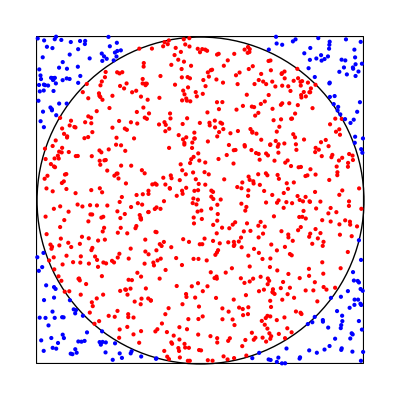

```mathematica
Graphics[
{EdgeForm[Black],FaceForm[White],Rectangle[{-1,-1},{1,1}],Circle[],
Red,Point[hitList],Blue,Point[missList]}
]
```